```mathematica
Needs["FourierSeries`"]
f[t_]:=Cos[t]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {4.81037×10^7}. NIntegrate obtained -0.10889+0.00209008 ⅈ and 0.32782 for the integral and error estimates.

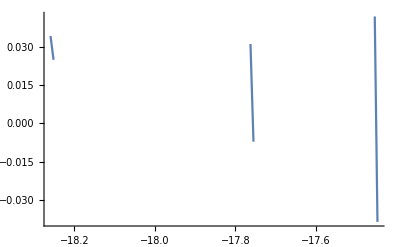

```mathematica
Plot[NFourierTransform[f[t],t, ω], {ω, -20,20}, PlotRange -> 0]
```